```mathematica
allGraphs5[lambdaKey,"colofour" ]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
EdgeList[gr]
```

{1<->2,1<->5,2<->3,3<->4,4<->5}

```mathematica
gr=Graph[EdgeAdd[VertexAdd[allGraphs5[lambdaKey,"graph" ],{6,7}],{1<->6,2<->6,5<->7}],VertexLabels->"Name"]
```

-Graphics-

```mathematica
EmbedGraphInGr[key_]:=Block[{val=allGraphs5[key], sets, g, sub},
sets=val["vertexsets"];
g=gr;
g=EdgeDelete[ g,{1<->2,1<->5,2<->3,3<->4,4<->5}];
Table[If[Length[s]>1,
g=VertexContract[g,s]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{First[sets[[e[[1]]]]]<->First[sets[[e[[2]]]]]}],{e,EdgeList[sub]}];

Graph[VertexList[g],EdgeList[g],VertexLabels->"Name"]
]
```

```mathematica
Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofour"]]]==2&]
```

{29523,29521,29529,29515,29517,29513,29542,29497,29506,29602,29577,29443,29446,29469,29417,29766,29737,29826,29677,29706,29648,29281,29282,29305,29257,29353,29378,29328,29209,29232,29186,30244,30172,30406,30010,30082,29938,28795,28804,28876,29038,29128,31708,31684,31924,31468,31492,31444,32198,30981,31224,27337,27340,27364,27580,27610,28065,28308,26609,26852,36084,36058,36138,36004,36030,35978,36736,35353,35434,38254,37548,33889,33916,34620,33158,22963,22964,22990,23044,23072,23689,23770,22237,22318,25141,25168,25868,24414,20785,20812,21510,20060,49206,49204,49212,49198,49200,49196,49954,48451,48460,51472,50718,46939,46942,47694,46184,56010,55252,57528,53734,54492,52976,42403,42404,43156,41650,44662,45416,43908,40144,40896,39392,9841,9842,9844,9850,9854,10543,10552,9139,9148,11947,11950,12650,11244,7735,7738,8436,7034,16159,16160,16864,15454,18274,18980,17568,14044,14748,13340,3523,3524,4222,2824,5620,6320,4920,1426,2124,728}

```mathematica
ListofVars[allGraphs5[29523,"colofour" ]]/.RepKey["C"]
```

{29525,29524}

```mathematica
ChromaticPolynomial[EmbedGraphInGr[29523],x]//Simplify
```

x (-6+11 x-6 x^2+x^3)^2

```mathematica
parts=Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[allGraphs5[29523,"colofour" ]]/.RepKey["C"])}]
```

{(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (-24+26 x-9 x^2+x^3)}

```mathematica
Total[parts]//Simplify
```

x (-6+11 x-6 x^2+x^3)^2

## Second example

```mathematica
Select[Keys[allGraphs5],35<Length[ListofVars[allGraphs5[#,"colofour"]]]&]
```

{0,19683,6561,2187,729,243,81,27,9,3,1}

```mathematica
ListofVars[allGraphs5[19683,"colofour" ]]/.RepKey["C"]
```

{39014,38308,38281,36898,36817,36194,36166,36112,36086,36085,32684,32441,31984,31954,31738,31714,31711,30586,30496,30334,30262,30253,29888,29857,29797,29768,29767,29633,29608,29605,29560,29551,29537,29533,29527,29525,29524}

```mathematica
ChromaticPolynomial[EmbedGraphInGr[19683],x]//Simplify
```

(-2+x) (-1+x)^2 x^4

```mathematica
parts=Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[allGraphs5[19683,"colofour" ]]/.RepKey["C"])}]
```

{(-2+x) (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (-24+26 x-9 x^2+x^3)}

```mathematica
Total[parts]//Simplify
```

(-2+x) (-1+x)^2 x^4

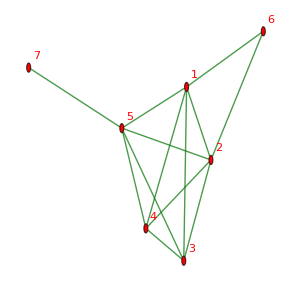

```mathematica
EmbedGraphInGr[K5Key]
```